```mathematica
ZTransform[(-2)^n *UnitStep[-n-1],n,z]
```

0

```mathematica
InverseZTransform[z/(z-a),z,n]
```

a^n

```mathematica
ZTransform[-a^n*UnitStep[-n-1],n,z,GenerateConditions->True]
```

0

```mathematica
F=ZTransform[1/3*(1/2)^(n-1)* UnitStep[n-1],n,z,GenerateConditions->True]
```

```mathematica
ConditionalExpression[2/(-3+6 z),Abs[z]>1/2]
```

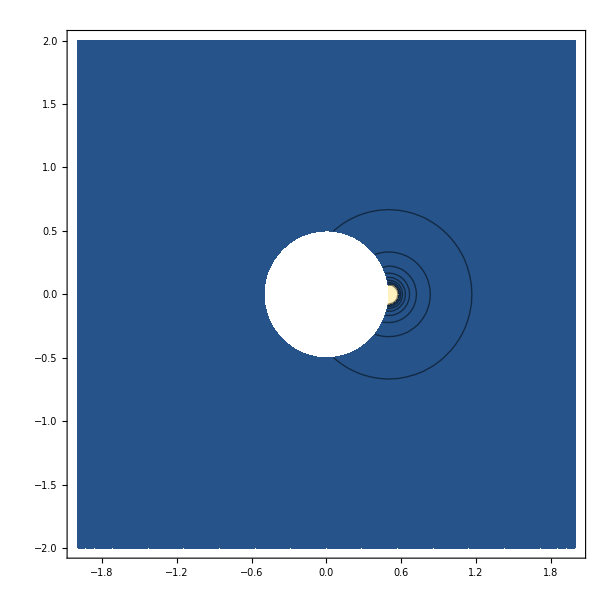
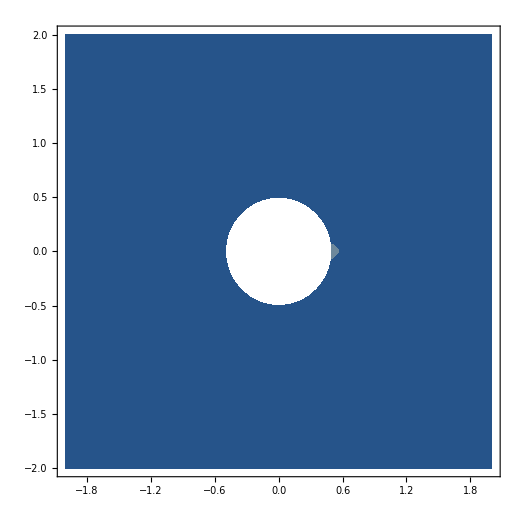
{-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
Block[{z=σ+I ω},Table[plot[Abs[F],{σ,-2,2},{ω,-2,2},PlotRange->All],{plot,{Plot3D,ContourPlot,DensityPlot}}]]
```

```mathematica
InverseZTransform[(1/3*z^-1/(1-1/2 z^-1)),z,n]
```

1/3 2^(1-n) UnitStep[-1+n]